```mathematica
B0=4.7*10^(-2);(*W g^−0.75*)
Em=5774;(*J/gram*)
a = B0/Em;
m0 = (.0558*(1/1000)^.92*M^0.92)*1000;
ϵLam = 0.95;
τLam = -Log[(1-ϵLam^(1/4))/(1 - (m0/M)^(1/4))]*(4*M^(1/4))/a;
ConsumerGrowth =(Log[2]/τLam) (*Fecundity = 2*)
```

-(1.41054×10^-6)/(M^(1/4) Log[0.0127415/(1-0.558031/M^0.02)])

```mathematica
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
ConsumerMortality = (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)
```

(3.20929×10^-8 (-1+ⅇ^(0.5858 M^0.03)))/M^0.59

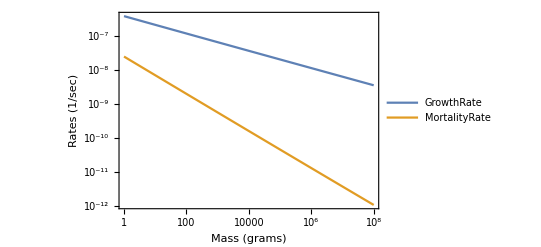

```mathematica
LogLogPlot[{ConsumerGrowth,ConsumerMortality},{M,1,10^8},Frame->True,FrameLabel->{"Mass (grams)","Rates (1/sec)"},PlotLegends->{"GrowthRate","MortalityRate"}]
```

```mathematica
BLam=1/(3 a)ⅇ^(-(a τLam)/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam)/M^(1/4))) m0+M (-48 ⅇ^((3 a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))-36 ⅇ^((a τLam)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2-16 ⅇ^((a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (-1+4 (m0/M)^(1/4)-6 √(m0/M)+4 (m0/M)^(3/4))+ⅇ^((a τLam)/M^(1/4)) (-25+12 (m0/M)^(1/4)+6 √(m0/M)+4 (m0/M)^(3/4)))+3 a ⅇ^((a τLam)/M^(1/4)) M^(3/4) τLam);
```

Some parameter settings for dynamic eqn:

```mathematica
(*s*)1,
(*M*)M,
(*B0*)4.7*10^(-2),
(*Em*)5774(*J/gram*),
(*η*)3/4,
(*γ*)1.19,
(*ζ*)1.00,
(*f0*)fatscale*0.0202,
(*mm0*)musclescale*0.383,
(*α*)(*2.10*10^(-9)*)(9.45*10^(-9)),
(*Ed*)18200,
(*c*)(*5*)23000,
(*k*)(*10*)23000/2,
```